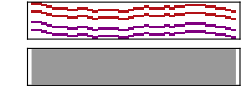

```mathematica
n=40;
T[x_]:=x+RandomChoice[{-1,0,1}];t=NestList[T,0,n];
a1=Table[SoundNote[{t[[k]],5+t[[k]]},{k,k+1},"Piano",SoundVolume->Sin[k/3]],{k,n}];
a2=Table[SoundNote[{12+t[[k]],17+t[[k]]},{k,k+1},"Flute",SoundVolume->Sin[k/2]],{k,n}];
Sound[Union[a1,a2],{0,6}]
```